Максимальный поток в сети: 67

Минимальный разрез сети S/T:{1,10,15,16,22,26,18,25,28,31,38,37,41}/{2,3,4,5,9,12,14,6,20,23,24,27,29,33,32,30,36,39,35,40,45}

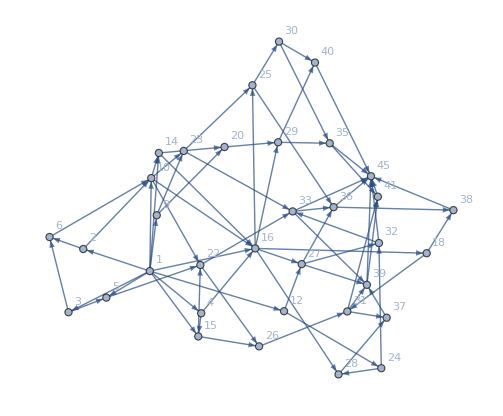

```mathematica
Unprotect[E];

E={{1,2,5},{1,3,11},{1,4,11},{1,5,4},{1,9,5},{1,10,11},{1,12,10},{1,14,12},{1,15,6},{1,16,6},{2,6,4},{2,10,11},{3,5,4},{3,6,11},{4,15,5},{4,16,7},{5,22,10},{6,10,10},{9,20,7},{9,23,10},{10,14,4},{10,16,11},{10,22,9},{10,23,4},{12,24,10},{12,27,5},{14,16,12},{14,20,6},{15,22,9},{15,26,5},{16,18,10},{16,25,11},{16,27,4},{16,28,9},{16,29,7},{18,31,10},{18,38,6},{20,29,4},{22,26,10},{22,33,8},{23,25,8},{23,33,9},{24,28,6},{24,32,9},{25,30,5},{25,36,12},{26,31,6},{27,32,9},{27,36,6},{27,39,6},{28,37,12},{29,35,4},{29,40,7},{30,35,11},{30,40,6},{31,37,5},{31,39,6},{31,41,8},{32,33,9},{32,45,6},{33,36,5},{33,39,10},{33,45,10},{35,41,6},{35,45,5},{36,38,9},{36,45,10},{37,39,4},{38,45,11},{39,41,12},{39,45,10},{40,45,12},{41,45,4}};

(*Edge lists*)
edgeList=Map[Function[x,DirectedEdge[Part[x,1],Part[x,2]]],E];
weights=Map[Function[x,Part[x,3]],E];
graph=Graph[edgeList,EdgeWeight->weights];

graph=SetProperty[graph,VertexLabels->"Name"];
graph=SetProperty[graph,GraphLayout->{VertexLayout->{"SpringElectricalEmbedding","EdgeWeighted"->True}}];
graph;
(*rested bandwidth matrix*)
R=E;(*
*)edgeCount=Length[R];

GetAdjacency[v_,findBackward_:False]:=Module[{},

adjacencyList={};
For[i=1,i≤edgeCount,i++,
If[R⟦i⟧⟦1⟧==v&&R⟦i⟧⟦3⟧≠0,AppendTo[adjacencyList,R⟦i⟧]];

If[findBackward,
If[R⟦i⟧⟦2⟧==v&&E⟦i⟧⟦3⟧-R⟦i⟧⟦3⟧>0,
bkw={R⟦i⟧⟦2⟧,R⟦i⟧⟦1⟧,E⟦i⟧⟦3⟧-R⟦i⟧⟦3⟧};
  AppendTo[adjacencyList,bkw];];
];
];

Return[adjacencyList];

]

SearchPath[vertex_,trg_,findBackward_,minFlow_:Infinity,visited_List:{},vPath_List:{}]:=Module[{i,resList,adjacencyList,locMinFlow,locVPath,locVisited,locFindBackward},

locFindBackward=findBackward;
locVPath=vPath;
locMinFlow=minFlow;
locVisited=visited;
resList={};
AppendTo[locVPath,vertex];
AppendTo[locVisited,vertex];
AppendTo[resList,locVisited];

(*if trg*)
If[vertex==trg,
(*return minFlow, path*)
AppendTo[resList,{True,locVPath,minFlow}];
,
(*go forward*)
AppendTo[resList,{False,locVPath,minFlow}];
adjacencyList=GetAdjacency[vertex,locFindBackward];

If[Length[adjacencyList]==0,
Return[resList]];

For[i=1,i<=Length[adjacencyList],i++,
If[MemberQ[locVPath,adjacencyList⟦i⟧⟦2⟧]||MemberQ[locVisited,adjacencyList⟦i⟧⟦2⟧],Continue[]];
locMinFlow=Min[minFlow,adjacencyList⟦i⟧⟦3⟧];
resList=SearchPath[adjacencyList⟦i⟧⟦2⟧,trg,locFindBackward,locMinFlow,locVisited,locVPath];
If[Length[resList]>1&&resList⟦2⟧⟦1⟧==True,Break[]];
locVisited=resList⟦1⟧;
];
];

Return[resList];
];(*END SEARCH*)

RecalcMatrix[R_List,vPath_List,minFlow_]:=Module[{i,j,locR},
locR=R;
For[i=1,i<Length[vPath],i++,
For[j=1,j≤Length[locR],j++,
If[vPath⟦i⟧==locR⟦j⟧⟦1⟧&&vPath⟦i+1⟧==locR⟦j⟧⟦2⟧,locR⟦j⟧⟦3⟧=locR⟦j⟧⟦3⟧-minFlow;];
(*slow down in backward edges*)
If[vPath⟦i⟧==locR⟦j⟧⟦2⟧&&vPath⟦i+1⟧==locR⟦j⟧⟦1⟧,locR⟦j⟧⟦3⟧=locR⟦j⟧⟦3⟧+minFlow;];
];
];
Return[locR];
]

pathList={};

src=1;
trg=45;
totalFlow=0;
backward=False;
(*Clear[GetAdjacency,RecalcMatrix,SearchPath];*)
Do[
maxIt=100;
While[maxIt>0,
res=SearchPath[src,trg,backward];
If[res⟦2⟧⟦1⟧,
AppendTo[pathList,{res⟦2⟧⟦2⟧,res⟦2⟧⟦3⟧}];
totalFlow=totalFlow+res⟦2⟧⟦3⟧;
R=RecalcMatrix[R,res⟦2⟧⟦2⟧,res⟦2⟧⟦3⟧];,
Break[];
];
maxIt--;
];
backward=!backward;
,{2}];


(*Min cut*)
S={1};
T=Delete[VertexList[graph],1];

For[i=1,i≤Length[S],i++,
For[j=1,j≤Length[R],j++,
If[R⟦j⟧⟦1⟧==S⟦i⟧&&R⟦j⟧⟦3⟧>0&&!MemberQ[S,R⟦j⟧⟦2⟧],
AppendTo[S,R⟦j⟧⟦2⟧];
For[k=1,k≤Length[T],k++,
If[T⟦k⟧==R⟦j⟧⟦2⟧,
T=Delete[T,k];Break[]];
];
];
];
];

Print["Максимальный поток в сети: ",totalFlow];
Print["Минимальный разрез сети S/T:",S,"/",T];

graph
```